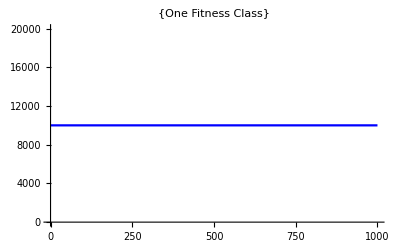

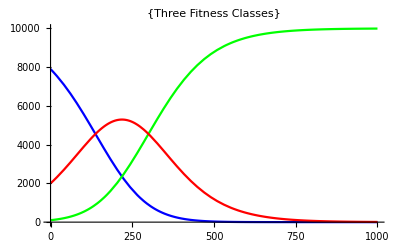

```mathematica
(* Testing SystemSolver, SolveDiffEqs *)
{Δc1,Δc2,popsize,timestep}={0.01,0.02,10^4,1000}; 
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-100-2000,100,2000};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Testing module that checks for new mutations, NextMutation *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep}={0,100}; 
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
```

```mathematica
getNextMutants[genotypes]
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,starttime,timestep]
```

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

{30.9401,{{1,4}},True,0.0393006,{{3,2}}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for first trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 6.13165 in Concurrent Mutations Regime with expected time scale 76.2333 and rate of adaptation 0.000131176

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m",results];
```

mean substitutional load = 0.0551617

mean q = 5.51617

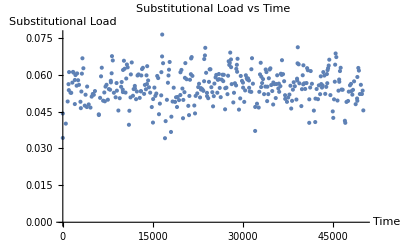

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m"];
meansubload1=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload1];
Print["mean q = ",meansubload1/Δc1];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for second trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,0 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Trait 2 q = 4.71143 in Concurrent Mutations Regime with expected time scale 71.3783 and rate of adaptation 0.000280197

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m",results];
```

mean substitutional load = 0.0798228

mean q = 3.99114

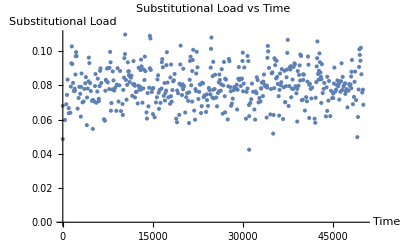

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m"];
meansubload2=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload2];
Print["mean q = ",meansubload2/Δc2];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store only summary data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 6.13165 in Concurrent Mutations Regime with expected time scale 76.2333 and rate of adaptation 0.000131176

Trait 2 q = 4.71143 in Concurrent Mutations Regime with expected time scale 71.3783 and rate of adaptation 0.000280197

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m",results];
```

mean substitution load = 0.0779544

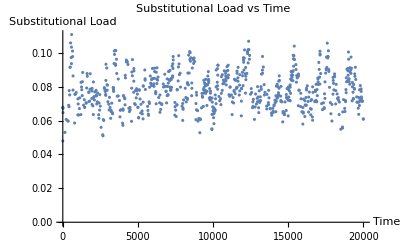

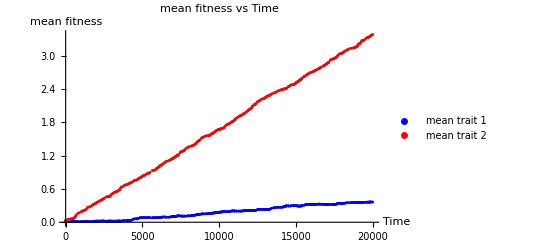

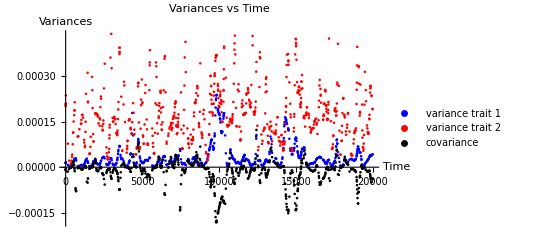

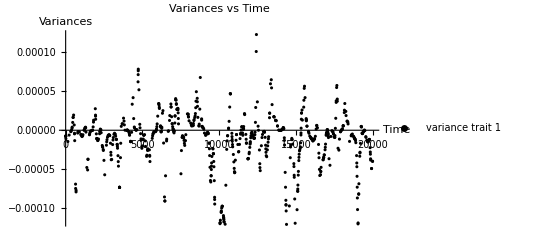

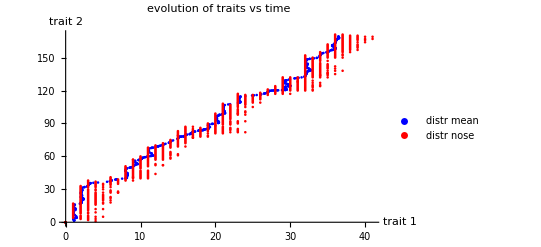

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Print["mean substitution load = ",meansubload];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{timesAndCov},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"evolution of traits vs time"]
```

```mathematica
(* Generate animation of details evolution of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
plots=Table[ListPlot[{mean2mean[[1;;i]],noseTravel[[1;;i]]},PlotStyle->{Black,Red},PlotRange->{{0,60},{0,150}},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->{"evolution of traits vs time"}],{i,1,Length[mean2mean]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi",plots]
```

~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.avi",plots];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data with equal trait parameters *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

Trait 2 q = 4. in Concurrent Mutations Regime with expected time scale 153.506 and rate of adaptation 0.0000651442

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m",results];
```

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"Evolution of blob"],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.avi",plots];
```

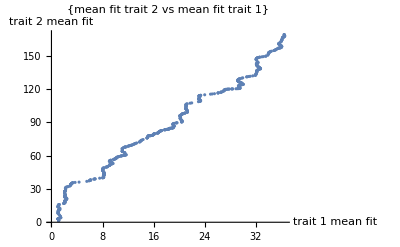

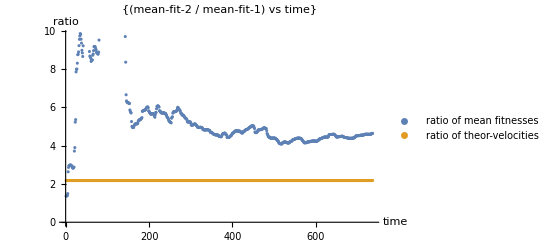

Total Fitness Increase = 3.74915 and predicted increase by theoretical sum of rate of increases is 6.03074

Trait 1 Fitness Increase = 0.364409 and predicted increase by theoretical rate of increase is 1.89607

Trait 2 Fitness Increase = 3.38475 and predicted increase by theoretical rate of increase is 4.13467

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
Print["Total Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 +mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical sum of rate of increases is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2+Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 1 Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 , " and predicted increase by theoretical rate of increase is ",(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 2 Fitness Increase = ",mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical rate of increase is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)maxtime ]
```

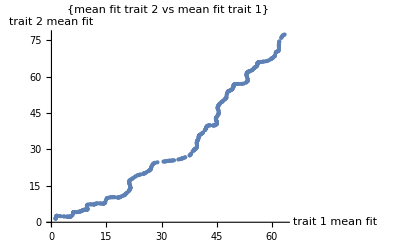

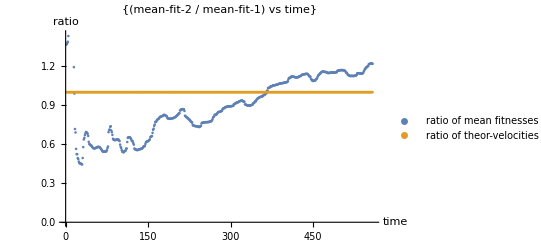

Total Fitness Increase = 1.4095 and predicted increase by theoretical sum of rate of increases is 2.60577

Trait 1 Fitness Increase = 0.635612 and predicted increase by theoretical rate of increase is 1.30288

Trait 2 Fitness Increase = 0.773886 and predicted increase by theoretical rate of increase is 1.30288

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp005.m"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
Print["Total Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 +mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical sum of rate of increases is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2+Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 1 Fitness Increase = ",mean2mean[[-1]][[1]]Δc1 , " and predicted increase by theoretical rate of increase is ",(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2)maxtime ]
Print["Trait 2 Fitness Increase = ",mean2mean[[-1]][[2]]Δc2 , " and predicted increase by theoretical rate of increase is ",(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)maxtime ]
```

```mathematica
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,60000};
{fulldata,verbose,veryverbose}={0,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run Simulations *)
ParallelDo[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat",results,"Data"];
Print["exp ",i];
,{i,2,35}];
```

0.647534

7.40436

0.087453

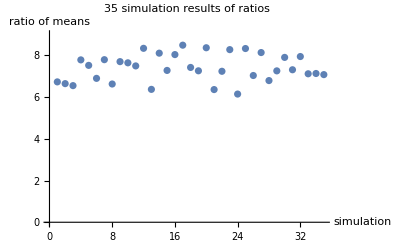

```mathematica
(* Analyzez convergence data *)
meanratios=Table[0,{i,1,35}];
Do[
results=Import["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat"];
meanratios[[i]]=results[[-1]][[3]]/results[[-1]][[2]];
,{i,1,35}];
StandardDeviation[meanratios]
Mean[meanratios]
StandardDeviation[meanratios]/Mean[meanratios]
ListPlot[meanratios,PlotRange->{0,9},PlotLabel->"35 simulation results of ratios",AxesLabel-> {"simulation","ratio of means"}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 a *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[10^(4+((j-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((j-1)/5))/popsize genotypeabundances][[2]][[1]];
simv[[j]]={(4+((j-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(4+((j-1)/5)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m",{simv,thryvest,simq,thryqest,thryqext}];
```

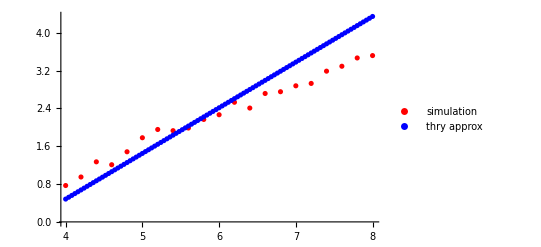

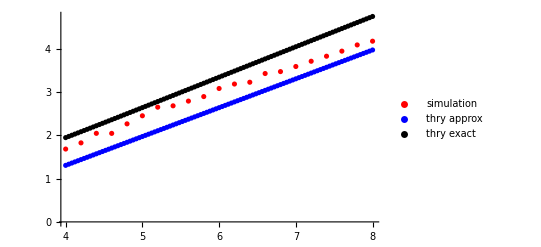

```mathematica
{simv,thryvest,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m"];
ListPlot[{simv,thryvest},PlotStyle->{Red,Blue},PlotLegends->{"simulation","thry approx"},Axes->True]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((j-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simq[[j]]={(-4-((j-1)/10)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m",{simq,thryqest,thryqext}];
```

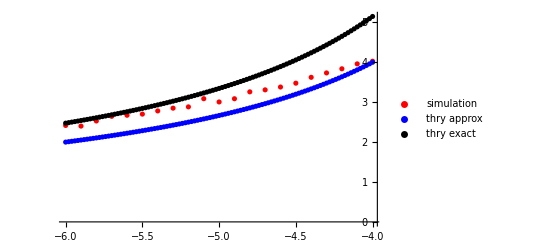

```mathematica
{simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m"];
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
Do[
results=RunSimulationCheckEachMutation2[10^4,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
,{j,1,21}];
```

```mathematica
results[[;;,9]]
```

{0.0242857,0.0201334,0.0106071,0.0198367,0.0193424,0.0100064,0.01,0.0198938,0.0191811,0.0201372,0.0164777,0.02446,0.0106283,0.0197502,0.0151301,0.0189631,0.0198868,0.0100395,0.019258,0.0110504,0.0197946,0.0102623,0.0177839,0.0156177,0.0196454,0.0176459,0.0199234,0.0198498,0.0250614,0.0195947,0.0199065,0.0190992,0.0144205,0.0197646,0.0195967,0.0194924,0.0190076,0.0255496,0.0195588,0.0198909,0.0210432,0.0298907,0.0250755,0.0191546,0.0280578,0.0287691,0.0192061,0.0193911,0.010007,0.0190055,0.0190686,0.011423,0.0138169,0.0100084,0.0159516,0.010501,0.019194,0.0101056,0.0198474,0.0199867,0.0108757,0.0143897,0.0106265,0.0193011,0.0114645,0.0174123,0.0190673,0.0143607,0.0123864,0.0194195,0.0151614,0.0151578,0.0151909,0.010019,0.0175153,0.028432,0.0290065,0.0100022,0.0127522,0.0149738,0.0187383,0.019666,0.0200325,0.0199962,0.0102727,0.0100006,0.01,0.01,0.0103906,0.0118271,0.0100046,0.0152327,0.0193058}